```mathematica
url="https://drive.google.com/open?id=15RjrWFWFBCTgOOLUPTVGeQD4VR4CUNtq&authuser=m160925%40g.unicamp.br&usp=drive_fs"
```

https://drive.google.com/open?id=15RjrWFWFBCTgOOLUPTVGeQD4VR4CUNtq&authuser=m160925%40g.unicamp.br&usp=drive_fs

```mathematica
durangodata = Import["G:\\Drives compartilhados\\Mestrado - Matheus\\Mathematica Script\\Paper - Arrhenius activation energy and transitivty in fission-track annealing equations\\DadosDurangoLcMod.CSV","Dataset","HeaderLines"->1]
```

```mathematica
lntempo=N[Log[Table[durangodata[[i,1]],{i,1,82}]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.693147,0.693147,2.30259,2.30259,2.30259,2.30259,2.30259,2.30259,2.30259,2.30259,2.30259,2.30259,2.30259,2.30259,2.30259,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,4.60517,6.90776,6.90776,6.90776,6.90776,6.90776,6.90776,6.90776,6.90776,6.90776,6.90776,6.90776,6.90776,6.90776,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685,27.0685}

```mathematica
temp=10^3(Table[durangodata[[i,6]],{i,1,82}])^-1
```

{2.51162,2.36323,2.36323,2.2314,2.22643,2.1046,2.00743,1.91516,1.9115,1.9115,1.821,1.74171,1.66903,1.60475,1.60475,1.60218,2.50532,2.36323,2.67989,2.51162,2.35766,2.2314,2.11349,2.1046,2.00743,1.9115,1.90785,1.90785,1.82432,1.74474,1.67182,2.87233,2.87233,2.67272,2.51162,2.50532,2.36323,2.2314,2.2314,2.1046,2.00743,2.00743,1.9115,1.9115,1.90785,1.90785,1.82432,1.82432,1.74474,2.67989,2.51162,2.36323,2.2314,2.11349,2.00743,1.9115,1.9115,1.9115,1.90785,1.82432,1.82432,1.82432,3.65509,3.61332,3.57035,3.50967,3.44105,3.4053,3.28506,3.27993,3.25661,3.19659,3.16824,3.14122,3.13708,3.11411,2.99607,2.97958,2.9418,2.89039,2.79869,2.78494}

```mathematica
durangoPsArrh=Table[{10^3/durangodata[[i,6]],N[Log[durangodata[[i,1]]]],durangodata[[i,7]]},{i,1,82}]
```

{{2.51162,0.,0.992736},{2.36323,0.,0.989104},{2.36323,0.,0.989709},{2.2314,0.,0.978814},{2.22643,0.,0.978814},{2.1046,0.,0.969128},{2.00743,0.,0.958838},{1.91516,0.,0.946731},{1.9115,0.,0.947337},{1.9115,0.,0.957022},{1.821,0.,0.918886},{1.74171,0.,0.881961},{1.66903,0.,0.821429},{1.60475,0.,0.720944},{1.60475,0.,0.71368},{1.60218,0.,0.702785},{2.50532,0.693147,0.989709},{2.36323,0.693147,0.991525},{2.67989,2.30259,0.997579},{2.51162,2.30259,0.996368},{2.35766,2.30259,0.984262},{2.2314,2.30259,0.964286},{2.11349,2.30259,0.961259},{2.1046,2.30259,0.9546},{2.00743,2.30259,0.946731},{1.9115,2.30259,0.921308},{1.90785,2.30259,0.912833},{1.90785,2.30259,0.920702},{1.82432,2.30259,0.880145},{1.74474,2.30259,0.800847},{1.67182,2.30259,0.716707},{2.87233,4.60517,0.99092},{2.87233,4.60517,0.992736},{2.67272,4.60517,0.994552},{2.51162,4.60517,0.981235},{2.50532,4.60517,0.984262},{2.36323,4.60517,0.98184},{2.2314,4.60517,0.958838},{2.2314,4.60517,0.965496},{2.1046,4.60517,0.928571},{2.00743,4.60517,0.923123},{2.00743,4.60517,0.921308},{1.9115,4.60517,0.863801},{1.9115,4.60517,0.87954},{1.90785,4.60517,0.888015},{1.90785,4.60517,0.868039},{1.82432,4.60517,0.783898},{1.82432,4.60517,0.800242},{1.74474,4.60517,0.652542},{2.67989,6.90776,0.989709},{2.51162,6.90776,0.978814},{2.36323,6.90776,0.958232},{2.2314,6.90776,0.952179},{2.11349,6.90776,0.929177},{2.00743,6.90776,0.871065},{1.9115,6.90776,0.808111},{1.9115,6.90776,0.846247},{1.9115,6.90776,0.779661},{1.90785,6.90776,0.792373},{1.82432,6.90776,0.697942},{1.82432,6.90776,0.671308},{1.82432,6.90776,0.684625},{3.65509,27.0685,0.889274},{3.61332,27.0685,0.900799},{3.57035,27.0685,0.883511},{3.50967,27.0685,0.901211},{3.44105,27.0685,0.906973},{3.4053,27.0685,0.893801},{3.28506,27.0685,0.900799},{3.27993,27.0685,0.878571},{3.25661,27.0685,0.892978},{3.19659,27.0685,0.874867},{3.16824,27.0685,0.860048},{3.14122,27.0685,0.86293},{3.13708,27.0685,0.864165},{3.11411,27.0685,0.84523},{2.99607,27.0685,0.818063},{2.97958,27.0685,0.811477},{2.9418,27.0685,0.816005},{2.89039,27.0685,0.816416},{2.79869,27.0685,0.777724},{2.78494,27.0685,0.75138}}

```mathematica
durangor9=Select[durangoPsArrh,(#[[3]]>.9)&];
```

```mathematica
durangor89=Select[durangoPsArrh,(0.8<#[[3]]<.9)&];
```

```mathematica
durangor89=Select[durangoPsArrh,(0.7<#[[3]]<.8)&]
durangor7=Select[durangoPsArrh,(#[[3]]<.7)&];
```

{{1.60475,0.,0.720944},{1.60475,0.,0.71368},{1.60218,0.,0.702785},{1.67182,2.30259,0.716707},{1.82432,4.60517,0.783898},{1.9115,6.90776,0.779661},{1.90785,6.90776,0.792373},{2.79869,27.0685,0.777724},{2.78494,27.0685,0.75138}}

```mathematica
durangor9[[;;,1;;2]]
```

{{2.51162,0.},{2.36323,0.},{2.36323,0.},{2.2314,0.},{2.22643,0.},{2.1046,0.},{2.00743,0.},{1.91516,0.},{1.9115,0.},{1.9115,0.},{1.821,0.},{2.50532,0.693147},{2.36323,0.693147},{2.67989,2.30259},{2.51162,2.30259},{2.35766,2.30259},{2.2314,2.30259},{2.11349,2.30259},{2.1046,2.30259},{2.00743,2.30259},{1.9115,2.30259},{1.90785,2.30259},{1.90785,2.30259},{2.87233,4.60517},{2.87233,4.60517},{2.67272,4.60517},{2.51162,4.60517},{2.50532,4.60517},{2.36323,4.60517},{2.2314,4.60517},{2.2314,4.60517},{2.1046,4.60517},{2.00743,4.60517},{2.00743,4.60517},{2.67989,6.90776},{2.51162,6.90776},{2.36323,6.90776},{2.2314,6.90776},{2.11349,6.90776},{3.61332,27.0685},{3.50967,27.0685},{3.44105,27.0685},{3.28506,27.0685}}

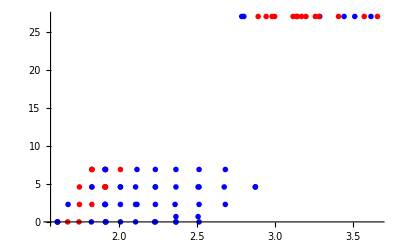

```mathematica
DurangoPoints=ListPlot[{Select[durangoPsArrh,(#[[3]]>.9)&][[;;,1;;2]],
Select[durangoPsArrh,(0.8<#[[3]]<.9)&][[;;,1;;2]],
Select[durangoPsArrh,(0.7<#[[3]]<.8)&][[;;,1;;2]],
Select[durangoPsArrh,(#[[3]]<.7)&][[;;,1;;2]]}
,PlotStyle->{Blue,Red,Blue,Red},PlotMarkers->{"OpenMarkers",10}]
```

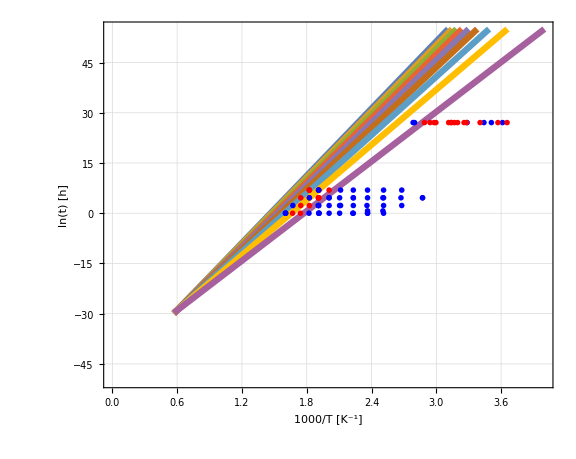

```mathematica
Show[pltPseudoArrhenius[[3]],DurangoPoints]
```